```mathematica
SetOptions[Plot,Frame->True,Axes->False,LabelStyle->{FontFamily->"Helvetica",FontSize->14}];SetOptions[ContourPlot,Frame->True,Axes->False,LabelStyle->{FontFamily->"Helvetica",FontSize->14}];
```

```mathematica
ϕ[n_,x_]=FullSimplify[((π^(1/4)*Sqrt[n!*2^n])^(-1))*HermiteH[n,x]*Exp[-(x^2)/2]]
```

(ⅇ^(-x^2/2) HermiteH[n,x])/(π^(1/4) √(2^n n!))

```mathematica
ϕ[0,x]
```

(ⅇ^(-x^2/2))/π^(1/4)

```mathematica
ϕ[1,x]
```

(√2 ⅇ^(-x^2/2) x)/π^(1/4)

```mathematica
ϕ[2,x]
```

(ⅇ^(-x^2/2) (-2+4 x^2))/(2 √2 π^(1/4))

```mathematica
Densityϕ[n_,x_]=Abs[ϕ[n,x]]^2
```

(2^(-Re[n]) ⅇ^(-Re[x^2]) Abs[HermiteH[n,x]]^2)/(√π Abs[n!])

```mathematica
IntegralDensityϕ[n_,region_,z_]=Piecewise[{{Integrate[Densityϕ[n,x],{x,-z,z},Assumptions->z∈Reals&&n∈Integers&&n>-1],region==1},{1-Integrate[Densityϕ[n,x],{x,-z,z},Assumptions->z∈Reals&&n∈Integers&&n>-1],region==-1}}];
```

```mathematica
IntegralProductϕ02[region_,z_]=Piecewise[{{Integrate[ϕ[0,x]*ϕ[2,x],{x,-z,z},Assumptions->z∈Reals],region==1},{Integrate[ϕ[0,x]*ϕ[2,x],{x,-Infinity,-z},Assumptions->z∈Reals]+Integrate[ϕ[0,x]*ϕ[2,x],{x,z,Infinity},Assumptions->z∈Reals],region==-1}}];
```

```mathematica
PNN[t_,a_,b_]=Piecewise[{{0,a==1&&b==1},{((1-t)^2),a==-1&&b==-1},{((t^2)/2) + (t*(1-t)),a==1&&b==-1},{((t^2)/2) + (t*(1-t)),a==-1&&b==1}}];
```

```mathematica
PNX[t_,a_,b_,z_]=Piecewise[{{((t^2/2)+t*(1-t))*IntegralDensityϕ[0,1,z],a==1&&b==1},{(t^2/2)*IntegralDensityϕ[2,-1,z]+(t*(1-t))*IntegralDensityϕ[1,-1,z]+((1-t)^2)*IntegralDensityϕ[0,-1,z],a==-1&&b==-1},{((t^2/2)+t*(1-t))*IntegralDensityϕ[0,-1,z],a==1&&b==-1},{(t^2/2)*IntegralDensityϕ[2,1,z]+(t*(1-t))*IntegralDensityϕ[1,1,z]+((1-t)^2)*IntegralDensityϕ[0,1,z],a==-1&&b==1}}];
```

```mathematica
PXX[t_,a_,b_,z_]=Piecewise[{{(t^2/2)*(2*IntegralDensityϕ[0,1,z]*IntegralDensityϕ[2,1,z]+2*(IntegralProductϕ02[1,z])^2) + t*(1-t)*(IntegralDensityϕ[1,1,z]*IntegralDensityϕ[0,1,z])+((1-t)^2)*(IntegralDensityϕ[0,1,z])^2,a==1&&b==1},{(t^2/2)*(2*IntegralDensityϕ[0,-1,z]*IntegralDensityϕ[2,-1,z]+2*(IntegralProductϕ02[-1,z])^2) + t*(1-t)*(IntegralDensityϕ[1,-1,z]*IntegralDensityϕ[0,-1,z])+((1-t)^2)*(IntegralDensityϕ[0,-1,z])^2,a==-1&&b==-1},{(t^2/2)*(IntegralDensityϕ[0,-1,z]*IntegralDensityϕ[2,1,z]+IntegralDensityϕ[2,-1,z]*IntegralDensityϕ[0,1,z]+2*(IntegralProductϕ02[1,z]*IntegralProductϕ02[-1,z]))+t*(1-t)*(IntegralDensityϕ[0,-1,z]*IntegralDensityϕ[1,1,z]+IntegralDensityϕ[1,-1,z]*IntegralDensityϕ[0,1,z])+((1-t)^2)*(IntegralDensityϕ[0,1,z]*IntegralDensityϕ[0,-1,z]),a==1&&b==-1},{(t^2/2)*(IntegralDensityϕ[0,-1,z]*IntegralDensityϕ[2,1,z]+IntegralDensityϕ[2,-1,z]*IntegralDensityϕ[0,1,z]+2*(IntegralProductϕ02[1,z]*IntegralProductϕ02[-1,z]))+t*(1-t)*(IntegralDensityϕ[0,-1,z]*IntegralDensityϕ[1,1,z]+IntegralDensityϕ[1,-1,z]*IntegralDensityϕ[0,1,z])+((1-t)^2)*(IntegralDensityϕ[0,1,z]*IntegralDensityϕ[0,-1,z]),a==-1&&b==1}}];
```

```mathematica
ENN[t_]=PNN[t,1,1]+PNN[t,-1,-1]-PNN[t,1,-1]-PNN[t,-1,1];
ENX[t_,z_]=PNX[t,1,1,z]+PNX[t,-1,-1,z]-PNX[t,1,-1,z]-PNX[t,-1,1,z];
EXN[t_,z_]=ENX[t,z];
EXX[t_,z_]=PXX[t,1,1,z]+PXX[t,-1,-1,z]-PXX[t,1,-1,z]-PXX[t,-1,1,z];
S[t_,z_]=EXX[t,z]+2*ENX[t,z]-ENN[t];
```

```mathematica
S[1,0.83]
```

2.24952

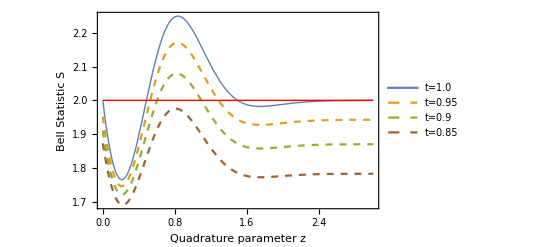

```mathematica
NoonTZPlot = Plot[{S[1.0,z],S[0.95,z],S[0.9,z],S[0.85,z],2.},{z,0.,3.},PlotLegends->Placed[LineLegend[{Style["t=1.0",Black,Plain,12],Style["t=0.95",Black,Plain,12],Style["t=0.9",Black,Plain,12],Style["t=0.85",Black,Plain,12]},Spacings->0.15],{0.8,0.77}],PlotStyle->{Thick,Dashed,Dashed,{Dashed,Brown},{Thin,Red}},FrameLabel->{"Quadrature parameter z","Bell Statistic S"}]
```

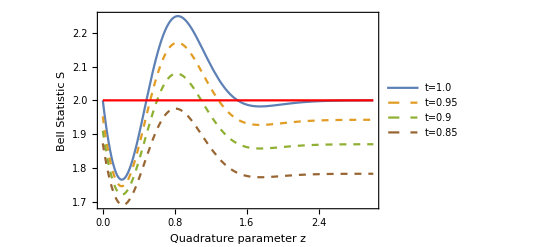

```mathematica
Show[NoonTZPlot]
```

```mathematica
Export["C:/Users/emlyn/Google Drive/Undergrad 5th year/Semester 2/Quantum Computing/NoonTZPlot.eps",NoonTZPlot]
```

C:/Users/emlyn/Google Drive/Undergrad 5th year/Semester 2/Quantum Computing/NoonTZPlot.eps

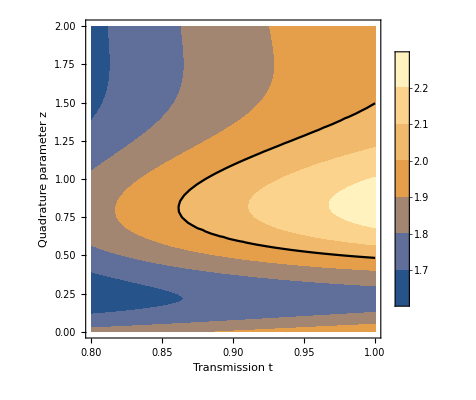

```mathematica
NoonContour=Show[ContourPlot[S[t,z], {t,0.8,1.0},{z,0.,2.}, PlotRange->All, PlotLegends->Automatic,ContourStyle->None,FrameLabel->{"Transmission t","Quadrature parameter z"}],ContourPlot[S[t,z]==2., {t,0.8,1.0},{z,0.,2.}, PlotRange->All, PlotLegends->Automatic,ContourStyle->Black]]
```

```mathematica
Export["C:/Users/emlyn/Google Drive/Undergrad 5th year/Semester 2/Quantum Computing/NoonContourPlot.eps",NoonContour]
```

C:/Users/emlyn/Google Drive/Undergrad 5th year/Semester 2/Quantum Computing/NoonContourPlot.eps

```mathematica
λ := λ = 0.83;
SumLimit := SumLimit = 200.;
SumLimit
```

200.

```mathematica
ScientificForm[200.]
```

2.×10^2

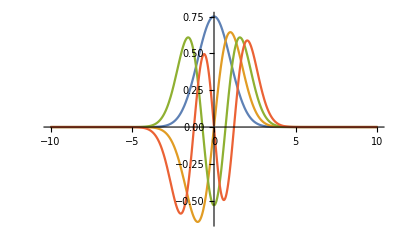

```mathematica
ϕ[n_,x_]:=ϕ[n,x]=FullSimplify[((π^(1./4.)*Sqrt[n!*2.^n])^(-1.))*HermiteH[n,x]*Exp[-(x^2.)/2.]]
Show[Plot[{ϕ[0,x],ϕ[1,x],ϕ[2,x],ϕ[3,x]},{x,-10,10},PlotRange->All]]
```

```mathematica
PXX[x_,y_]:=PXX[x,y]=(1/π)*FullSimplify[Exp[((x^2+y^2)*(1+λ^2)-4*x*y*λ)/((λ^2-1))]]
```

```mathematica
ϕθ[n_,y_,θ_]:=ϕθ[n,y,θ]=FullSimplify[((π^(1./4.)*Sqrt[n!*2.^n])^(-1))*HermiteH[n,y]*Exp[-(y^2.)/2.]*Exp[-ⅈ*θ*n]]
```

```mathematica
PXXtheta[x_,y_,θ_]:=PXXtheta[x,y,θ]=FullSimplify[ComplexExpand[FullSimplify[(((1-λ^2)*Exp[-x^2-y^2])/(π*(Abs[Sqrt[1-(λ^2)*Exp[-2*ⅈ*θ]]]^2)))*Abs[Exp[((λ^2)*Exp[-2*ⅈ*θ]*(x^2+y^2)-2*λ*x*y*Exp[-ⅈ*θ])/((λ^2)*Exp[-2*ⅈ*θ]-1)]]^2,Assumptions->x∈Reals&&y∈Reals&&θ∈Reals&&λ∈Reals&&0≤ λ≤ 1]]]
PXXtheta[x,y,θ]
```

(0.0990262 ⅇ^((0.381345 x^2+0.381345 y^2-0.749639 x y Cos[θ])/(-1.07024+1. Cos[2 θ])))/(√(1.47458-1.3778 Cos[2 θ]))

```mathematica
E1X[x_]=FullSimplify[(1.-λ^2.)*(π^(-1/2))*Exp[-x^2]*(((1.-λ^4.)^(-1/2))*Exp[((λ^2.)*((λ^2.)*(2*x^2.)-2*x^2.))/(λ^4. - 1)]-HermiteH[0,x]^2)];
E0X[x_]=(1.-λ^2.)*Abs[ϕ[0,x]]^2.
```

0.175519 (ⅇ^(-0.5 Re[x^2.]))^2.

```mathematica
ENN = RealAbs[Sum[(1.-λ^2.)*λ^(2.*n),{n,0,Infinity}]]
```

1.

```mathematica
PNX[1,1,z_?NumericQ]:=PNX[1,1,z]=NIntegrate[E1X[x],{x,-z,z}];
PNX[1,-1,z_?NumericQ]:=PNX[1,-1,z]=NIntegrate[E1X[x],{x,-Infinity,-z}]+NIntegrate[E1X[x],{x,z,Infinity}];
PNX[-1,1,z_?NumericQ]:=PNX[-1,1,z]=NIntegrate[E0X[x],{x,-z,z}];
PNX[-1,-1,z_?NumericQ]:=PNX[-1,-1,z]=NIntegrate[E0X[x],{x,-Infinity,-z}]+NIntegrate[E0X[x],{x,z,Infinity}];
FullSimplify[PNX[1,1,1]+PNX[-1,-1,1]+PNX[1,-1,1]+PNX[-1,1,1]]
ENX[z_?NumericQ]:=ENX[z]=PNX[1,1,z]+PNX[-1,-1,z]-PNX[1,-1,z]-PNX[-1,1,z];
```

1.

```mathematica
ProbXX[1,1,z_,θ_]:=NIntegrate[PXXtheta[x,y,θ],{x,-z,z},{y,-z,z}];
```

```mathematica
ProbXX[-1,1,z_,θ_]:=NIntegrate[PXXtheta[x,y,θ],{x,-Infinity,-z},{y,-z,z}]+NIntegrate[PXXtheta[x,y,θ],{x,z,Infinity},{y,-z,z}];
```

```mathematica
ProbXX[1,-1,z_,θ_]:=NIntegrate[PXXtheta[x,y,θ],{x,-z,z},{y,-Infinity,-z}]+NIntegrate[PXXtheta[x,y,θ],{x,-z,z},{y,z,Infinity}];
```

```mathematica
ProbXX[-1,-1,z_,θ_]:=NIntegrate[PXXtheta[x,y,θ],{x,-Infinity,-z},{y,-Infinity,-z}]+NIntegrate[PXXtheta[x,y,θ],{x,-Infinity,-z},{y,z,Infinity}]+NIntegrate[PXXtheta[x,y,θ],{x,z,Infinity},{y,-Infinity,-z}]+NIntegrate[PXXtheta[x,y,θ],{x,z,Infinity},{y,z,Infinity}];
```

```mathematica
FullSimplify[ProbXX[1,1,1,π/2]+ProbXX[-1,-1,1,π/2]+ProbXX[1,-1,1,π/2]+ProbXX[-1,1,1,π/2]]
EXX[z_,θ_]:=ProbXX[1,1,z,θ]+ProbXX[-1,-1,z,θ]-ProbXX[1,-1,z,θ]-ProbXX[-1,1,z,θ];
```

1.

```mathematica
S[z_?NumericQ,θ_?NumericQ]:=RealAbs[FullSimplify[EXX[z,θ]+2*ENX[z]-1.]];
S[0.86,π/2]
```

2.05252

```mathematica
globalmax = Maximize[{S[z,θ],0≤ z≤ 10, 0 ≤ θ ≤ N[π/2.]},{θ,z}]
```

{2.05252,{θ→1.5708,z→0.858112}}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{π/32,1.37285},{π/16,1.44282},{(3 π)/32,1.52988},{π/8,1.61719},{(5 π)/32,1.69707},{(3 π)/16,1.76731},{(7 π)/32,1.82792},{π/4,1.87957},{(9 π)/32,1.9231},{(5 π)/16,1.95931},{(11 π)/32,1.98887},{(3 π)/8,2.01233},{(13 π)/32,2.03015},{(7 π)/16,2.04266},{(15 π)/32,2.05007},{π/2,2.05252},{(17 π)/32,2.05007},{(9 π)/16,2.04266},{(19 π)/32,2.03015},{(5 π)/8,2.01233},{(21 π)/32,1.98887},{(11 π)/16,1.95931},{(23 π)/32,1.9231},{(3 π)/4,1.87957},{(25 π)/32,1.82792},{(13 π)/16,1.76731},{(27 π)/32,1.69707},{(7 π)/8,1.61719},{(29 π)/32,1.52988},{(15 π)/16,1.44282},{(31 π)/32,1.37285},{π,1.34443}}

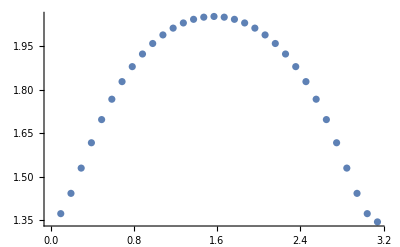

```mathematica
Maxima = Table[{n*π/32,FindMaxValue[{S[z,n*π/32],0≤ z≤ 10},z]},{n, 32}]
ListPlot[Maxima]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

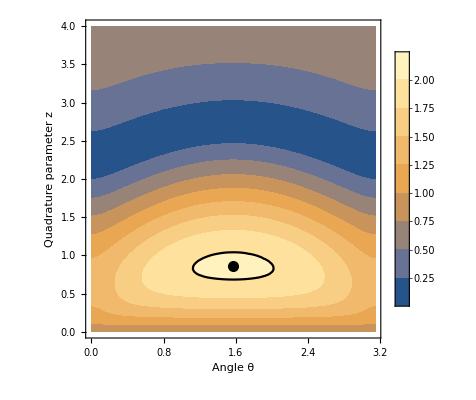

```mathematica
TMSSContour = Show[ContourPlot[S[z,θ], {θ,0.,N[π]},{z,0.,4.},Epilog->{PointSize[0.02],Black,Point[{θ,z}/.Last[globalmax]]},PlotRange->All, PlotLegends->Automatic,ContourStyle->None,FrameLabel->{"Angle θ","Quadrature parameter z"}],ContourPlot[S[z,θ]==2., {θ,0.,N[π]},{z,0.,4.}, PlotRange->All, PlotLegends->Automatic,ContourStyle->Black]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

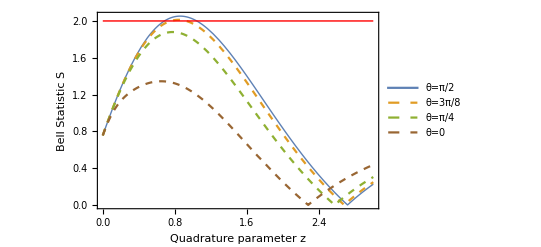

```mathematica
SSTthetaPlot = Plot[{S[z,π/2.],S[z,3.π/8.],S[z,π/4.],S[z,0.],2.},{z,0.,3.},PlotLegends->Placed[LineLegend[{Style["θ=π/2",Black,Plain,12],Style["θ=3π/8",Black,Plain,12],Style["θ=π/4",Black,Plain,12],Style["θ=0",Black,Plain,12]},Spacings->0.15],{0.83,0.65}],PlotStyle->{Thick,Dashed,Dashed,{Dashed,Brown},{Thin,Red}},FrameLabel->{"Quadrature parameter z","Bell Statistic S"}]
```

```mathematica
Export["C:/Users/emlyn/Google Drive/Undergrad 5th year/Semester 2/Quantum Computing/SSPlot.eps",SSTthetaPlot]
```

C:/Users/emlyn/Google Drive/Undergrad 5th year/Semester 2/Quantum Computing/SSPlot.eps

```mathematica
Export["C:/Users/emlyn/Google Drive/Undergrad 5th year/Semester 2/Quantum Computing/SSContourPlot.eps",TMSSContour]
```

C:/Users/emlyn/Google Drive/Undergrad 5th year/Semester 2/Quantum Computing/SSContourPlot.eps

```mathematica
ϕ[n_,x_]=FullSimplify[((π^(1/4)*Sqrt[n!*2^n])^(-1))*HermiteH[n,x]*Exp[-(x^2)/2]]
```

(ⅇ^(-x^2/2) HermiteH[n,x])/(π^(1/4) √(2^n n!))

```mathematica
PN[1]=1/2;
PN[1]=1/2;
PNN[1,1]=0;
PNN[0,0]=0;
PNN[1,0]=1/2;
PNN[0,1]=1/2
```

1/2

```mathematica
PNX[1,1,z_]=0.5*Integrate[ϕ[0,x]^2,{x,-z,z},Assumptions->z∈Reals];
PNX[1,0,z_]=0.5*(Integrate[ϕ[0,x]^2,{x,-Infinity,-z},Assumptions->z∈Reals]+Integrate[ϕ[0,x]^2,{x,z,Infinity},Assumptions->z∈Reals]);
PNX[0,0,z_]=0.5*(Integrate[ϕ[1,x]^2,{x,-Infinity,-z},Assumptions->z∈Reals]+Integrate[ϕ[1,x]^2,{x,z,Infinity},Assumptions->z∈Reals]);
PNX[0,1,z_]=0.5*Integrate[ϕ[1,x]^2,{x,-z,z},Assumptions->z∈Reals]
```

0.5 (-(2 ⅇ^(-z^2) z)/(√π)+Erf[z])

```mathematica
PXN[1,1,z_]=PNX[1,1,z];
PXN[0,0,z_]=PNX[0,0,z];
PXN[1,0,z_]=PNX[0,1,z];
PXN[0,1,z_]=PNX[1,0,z]
```

0.5 Erfc[z]

```mathematica
PNP[1,1,z_]=PNX[1,1,z];
PNP[1,0,z_]=PNX[1,0,z];
PNP[0,1,z_]=PNX[0,1,z];
PNP[0,0,z_]=PNX[0,0,z];
PPN[1,1,z_]=PXN[1,1,z];
PPN[1,0,z_]=PXN[1,0,z];
PPN[0,1,z_]=PXN[0,1,z];
PPN[0,0,z_]=PXN[0,0,z]
```

0.5 ((2 ⅇ^(-z^2) z)/(√π)+Erfc[z])

```mathematica
PXXIntegrand[x_,y_] = (ϕ[0,x]^2)*(ϕ[1,y]^2)+(ϕ[0,y]^2)*(ϕ[1,x]^2)+2*ϕ[0,x]*ϕ[1,x]*ϕ[0,y]*ϕ[1,y];
PXX[1,1,z_]=0.5*Integrate[PXXIntegrand[x,y],{x,-z,z},{y,-z,z},Assumptions->z∈Reals];
PXX[1,0,z_]=0.5*Integrate[PXXIntegrand[x,y],{x,-z,z},{y,-Infinity,-z},Assumptions->z∈Reals]+0.5*Integrate[PXXIntegrand[x,y],{x,-z,z},{y,z,Infinity},Assumptions->z∈Reals];
PXX[0,1,z_]=PXX[1,0,z];
PXX[0,0,z_]=1-PXX[1,1,z]-PXX[1,0,z]-PXX[0,1,z];
PPP[1,1,z_]=PXX[1,1,z];
PPP[1,0,z_]=PXX[1,0,z];
PPP[0,1,z_]=PXX[0,1,z];
PPP[0,0,z_]=PXX[0,0,z]
```

1-1. Erf[z] (-(2 ⅇ^(-z^2) z)/(√π)+Erf[z])-2. (Erf[z] Erfc[z]+(ⅇ^(-z^2) (z-2 z Erfc[z]))/(√π))

```mathematica
PXPIntegrand[x_,p_]=Abs[ϕ[0,x]^2+ϕ[1,x]^2]*Abs[ϕ[0,p]^2+ϕ[1,p]^2];
PXP[1,1,z_]=0.25*Integrate[PXPIntegrand[x,p],{x,-z,z},{p,-z,z},Assumptions->z∈Reals&&z>0];
PXP[1,0,z_]=0.25*Integrate[PXPIntegrand[x,p],{x,-z,z},{p,-Infinity,-z},Assumptions->z∈Reals&&z>0]+0.25*Integrate[PXPIntegrand[x,p],{x,-z,z},{p,z,Infinity},Assumptions->z∈Reals&&z>0];
PXP[0,1,z_]=0.25*Integrate[PXPIntegrand[x,p],{x,-Infinity,-z},{p,-z,z},Assumptions->z∈Reals&&z>0]+0.25*Integrate[PXPIntegrand[x,p],{x,z,Infinity},{p,-z,z},Assumptions->z∈Reals&&z>0];
PXP[0,0,z_]=1-PXP[1,1,z]-PXP[1,0,z]-PXP[0,1,z];
PPX[1,1,z_]=PXP[1,1,z];
PPX[1,0,z_]=PXP[0,1,z];
PPX[0,1,z_]=PXP[1,0,z];
PPX[0,0,z_]=PXP[0,0,z]
```

1-0.31831 ⅇ^(-2 z^2) (-z+ⅇ^(z^2) √π Erf[z])^2-0.63662 ⅇ^(-2 z^2) (-z+ⅇ^(z^2) √π Erf[z]) (z+ⅇ^(z^2) √π Erfc[z])

```mathematica
S[z_]=FullSimplify[PN[1]+PN[1]-PNN[1,1]-2*PNX[1,1,z]-2*PNP[1,1,z]-PXX[1,1,z]+2*PXP[1,1,z]]
```

1.+0.63662 ⅇ^(-2 z^2) z^2+(-2.-1.12838 ⅇ^(-z^2) z+1. Erf[z]) Erf[z]

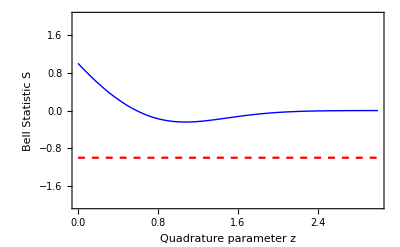

```mathematica
SingletPlot=Show[Plot[S[z],{z,0,3},Frame->True,PlotRange->{{0,3},{-2,2}},AxesOrigin->{0,3}, PlotPoints->50, MaxRecursion->2,PlotStyle->{Thick,Blue},FrameLabel->{"Quadrature parameter z","Bell Statistic S"}],Plot[-1,{z,0,3},Frame->True,PlotRange->{{0,3},{-2,2}},AxesOrigin->{0,3},PlotStyle->{Dashed,Red}]]
```

```mathematica
Export["C:/Users/emlyn/Google Drive/Undergrad 5th year/Semester 2/Quantum Computing/SingletPlot.eps",SingletPlot]
```

C:/Users/emlyn/Google Drive/Undergrad 5th year/Semester 2/Quantum Computing/SingletPlot.eps